```mathematica
mW=10^-3;
uW=10^-6;
ampDDS={
0.02,0.05,0.07,0.09,.11,.113,.13,.14,.15,.16,.17,.18,.19,.2,.21,.22,.23,.24,.25,.26,.27,.28
};

power={
26.3uW,

167uW,

330uW,

550uW,

815uW,

865uW,

1.134mW,

1.319mW,

1.502mW,

1.71mW,

1.93mW,

2.16mW,

2.4mW,

2.65mW,

2.92mW,

3.2mW,

3.49mW,

3.8mW,

4.1mW,

4.4mW,

4.75mW,

5.16mW
};
data=Thread[{power, ampDDS}];
```

{b→3.88988}

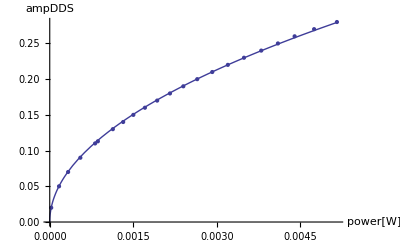

3.88988 √x

```mathematica
fitfn=b √x;
fit=FindFit[data,fitfn,b,x]
Show[
{Plot[fitfn/.fit,{x,0,power[[-1]]},AxesLabel->{"power[W]","ampDDS"}],
ListPlot[data]
}]

fitfn/.fit
```

(ⅇ^(-1/18 (-10.5+t)^2))/(3 √(2 π))

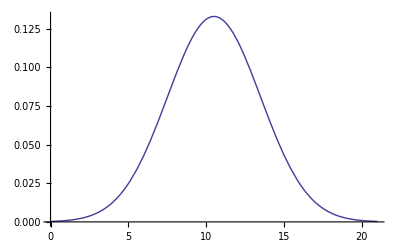

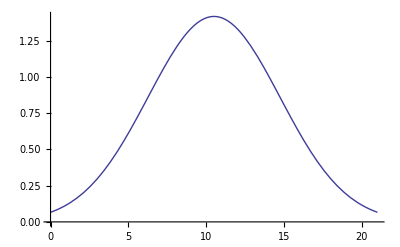

```mathematica
A=1;
σ=3;
t0=3.5σ;
pt=A/(σ √(2π)) Exp[-(t-t0)^2/(2 σ^2)]
Plot[pt,{t,0,7σ}]
Plot[fitfn/.fit/.x->pt,{t,0,7σ}]
```

```mathematica
Clear[A,σ,t0]
Integrate[A/(σ √(2π)) Exp[-(t-t0)^2/(2 σ^2)],{t,-Infinity,Infinity}]

(*pulse area = A, so set A to be 130us x however many uW..*)
```

ConditionalExpression[A/(√(1/σ^2) σ),Re[1/σ^2]≥0]